```mathematica
ClearAll["Global`*"];
```

```mathematica
f[x_,u_,v_]:=v;
g[x_,u_,v_]:=v-2u+x;
u10=0;
v10=1;
x0=0;
xf=1;
```

```mathematica
n=1000;
x=Table[j,{j,1,n+1}];
u1=Table[j,{j,1,n+1}];
v1=Table[j,{j,1,n+1}];
x[[1]]=x0;
u1[[1]]=u10;
v1[[1]]=v10;
h=(xf-x0)/n;
For[i=1,i<n+1,i++,
{
k1=h*f[x[[i]],u1[[i]],v1[[i]]];
l1=h*g[x[[i]],u1[[i]],v1[[i]]];
k2=h*f[x[[i]]+0.5*h,u1[[i]]+k1,v1[[i]]+l1];
l2=h*g[x[[i]]+0.5*h,u1[[i]]+k1,v1[[i]]+l1];
k3=h*f[x[[i]]+0.5*h,u1[[i]]+k2,v1[[i]]+l2];
l3=h*g[x[[i]]+0.5*h,u1[[i]]+k2,v1[[i]]+l2];
k4=h*f[x[[i]]+h,u1[[i]]+k3,v1[[i]]+l3];
l4=h*g[x[[i]]+h,u1[[i]]+k3,v1[[i]]+l3];
x[[i+1]]=x[[i]]+h;
u1[[i+1]]=u1[[i]]+(1/6)*(k1+2*k2+2*k3+k4);
v1[[i+1]]=v1[[i]]+(1/6)*(l1+2*l2+2*l3+l4);
}];
```

```mathematica
datau1=Transpose[{x,u1}];
datav1=Transpose[{x,v1}];
```

```mathematica
u20=1;
v20=2;
```

```mathematica
u2=Table[j,{j,1,n+1}];
v2=Table[j,{j,1,n+1}];
u2[[1]]=u20;
v2[[1]]=v20;
h=(xf-x0)/n;
For[i=1,i<n+1,i++,
{
k1=h*f[x[[i]],u2[[i]],v2[[i]]];
l1=h*g[x[[i]],u2[[i]],v2[[i]]];
k2=h*f[x[[i]]+0.5*h,u2[[i]]+k1,v2[[i]]+l1];
l2=h*g[x[[i]]+0.5*h,u2[[i]]+k1,v2[[i]]+l1];
k3=h*f[x[[i]]+0.5*h,u2[[i]]+k2,v2[[i]]+l2];
l3=h*g[x[[i]]+0.5*h,u2[[i]]+k2,v2[[i]]+l2];
k4=h*f[x[[i]]+h,u2[[i]]+k3,v2[[i]]+l3];
l4=h*g[x[[i]]+h,u2[[i]]+k3,v2[[i]]+l3];
x[[i+1]]=x[[i]]+h;
u2[[i+1]]=u2[[i]]+(1/6)*(k1+2*k2+2*k3+k4);
v2[[i+1]]=v2[[i]]+(1/6)*(l1+2*l2+2*l3+l4);
}];
```

```mathematica
datau2=Transpose[{x,u2}];
datav2=Transpose[{x,v2}];
```

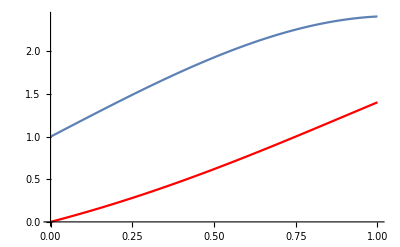

```mathematica
Show[{ListLinePlot[datau1,PlotStyle->Red]},
{ListLinePlot[datau2]},Mesh->All,AxesOrigin->{0,0},PlotRange->Automatic]
```

```mathematica
u1[[n+1]]
v1[[n+1]]
```

1.40372

1.60724

```mathematica
u2[[n+1]]
v2[[n+1]]
```

2.41126

0.199298

```mathematica
sol=Flatten[Solve[m*u1[[n+1]]+(1-m)*u2[[n+1]]+m*v1[[n+1]]+(1-m)*v2[[n+1]]==-E,m]];
```

```mathematica
lambda=m/.%[[1]]
```

-13.3088

```mathematica
u=lambda*u1+(1-lambda)*u2;
```

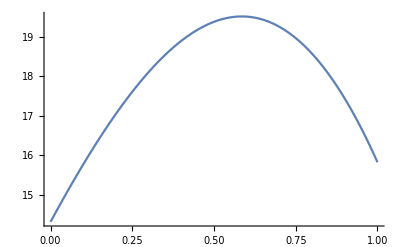

```mathematica
datau=Transpose[{x,u}];
ListLinePlot[datau]
```

{{y→Function[{x},-1/(8 √ⅇ (√7 Cos[(√7)/2]-Sin[(√7)/2]))(-2 √(7 ⅇ) Cos[(√7)/2]-4 √(7 ⅇ) x Cos[(√7)/2]+4 √7 ⅇ^(1+x/2) Cos[(√7 x)/2]+5 √7 ⅇ^(x/2) Cos[(√7 x)/2]+3 √7 ⅇ^(1/2+x/2) Cos[(√7)/2] Cos[(√7 x)/2]+2 √ⅇ Sin[(√7)/2]+4 √ⅇ x Sin[(√7)/2]+9 ⅇ^(1/2+x/2) Cos[(√7 x)/2] Sin[(√7)/2]+4 ⅇ^(1+x/2) Sin[(√7 x)/2]+5 ⅇ^(x/2) Sin[(√7 x)/2]-9 ⅇ^(1/2+x/2) Cos[(√7)/2] Sin[(√7 x)/2]+3 √7 ⅇ^(1/2+x/2) Sin[(√7)/2] Sin[(√7 x)/2])]}}

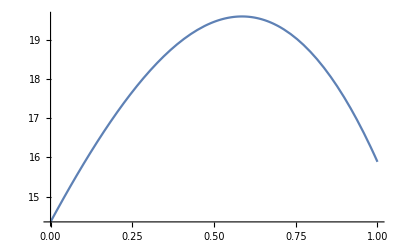

```mathematica
ClearAll["Global`*"];
sol=DSolve[{y''[x]-y'[x]+2*y[x]==x,y[0]-y'[0]==-1,y[1]+y'[1]==-E},y,x]
Plot[y[x]/.sol,{x,0,1}]
```